```mathematica
DupQ[list_]:=Length[list]≠Length[DeleteDuplicates[list]]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
KSubsets[
```

```mathematica
Subsets[
```

```mathematica
tf[x_]:=Piecewise[{{Piecewise[{{1, x==True}, {0, x==False}}], BooleanQ[x]==True}, {0, BooleanQ[x]==False}}]
```

```mathematica
RandomInteger[{1,100},RandomInteger[{1,50}]]
```

{44,10,16,3,36,66,30,50,64,36,16,86,54,71}

```mathematica
Timing[sset=DeleteCases[Monitor[Table[Block[{set=RandomInteger[{1,100},RandomInteger[{1,50}]]},Block[{T=Total[set]},Piecewise[{{Block[{T2=Total[Map[tf[Total[#]==T/2]&,Subsets[set,{2}]]]},Piecewise[{{set, T2>0}, {0, T2≤0}}]], EvenQ[T]==True}, {0, EvenQ[T]==False}}]]],{i,1,1000000}],i],0];Length[sset]]
```

$Aborted

```mathematica
Timing[mset=Monitor[Table[Block[{set=RandomInteger[{1,10},8]},Block[{T=Total[set]},Piecewise[{{Block[{T2=Total[Map[tf[Total[#]==T/2]&,Subsets[set,{2}]]]},Piecewise[{{minmod[set,1], T2>0}, {minmod[set,0], T2≤0}}]], EvenQ[T]==True}, {minmod[set,0], EvenQ[T]==False}}]]],{i,1,1000000}],i]]
```

{527.32272,{{0,2,{4,7,8,9,1,2,9,5}},{0,2,{8,1,5,7,6,1,2,9}},{0,5,{7,3,6,2,8,5,3,10}},{0,2,{2,4,6,7,7,9,9,3}},{0,2,{7,7,2,8,5,5,3,8}},{0,2,{3,5,7,7,10,8,1,2}},{0,2,{1,9,1,7,9,6,8,4}},{0,2,{8,7,2,8,8,10,8,7}},{0,2,{4,4,9,4,4,2,10,6}},{0,2,{9,9,4,8,4,5,4,10}},{0,2,{10,3,6,4,2,8,9,5}},{0,2,{6,6,3,1,9,6,4,10}},{0,2,{4,7,3,1,3,10,1,7}},999975,{0,2,{6,10,10,8,8,2,8,2}},{0,2,{8,3,10,3,2,8,1,10}},{0,2,{6,7,6,10,7,9,2,8}},{0,3,{6,9,2,4,10,7,1,1}},{0,2,{2,6,1,4,5,8,7,2}},{0,2,{2,4,10,6,9,2,6,4}},{0,2,{7,1,7,3,4,3,3,9}},{0,2,{4,3,8,10,7,6,3,2}},{0,2,{8,4,8,4,7,2,2,8}},{0,3,{8,8,3,1,3,6,3,6}},{0,2,{8,6,2,5,8,5,6,7}},{0,3,{4,7,9,2,9,9,6,10}}}}
 |  |  |  |

```mathematica
Map[#[[2]]/Total[#[[3]]]&,mset]
```

{2/45,2/39,5/44,2/47,2/45,2/43,2/45,1/29,2/43,2/53,2/47,2/45,1/18,2/55,5/52,1/14,2/43,1/21,2/55,2/35,1/16,1/19,2/43,2/37,2/51,2/37,2/45,3/52,3/44,2/39,2/37,1/16,2/47,2/51,1/16,2/41,7/52,2/39,1/23,2/49,2/41,1/12,2/61,7/38,3/40,2/35,1/24,5/56,5/48,2/45,5/46,2/51,2/39,2/31,2/37,7/38,3/34,2/41,1/24,2/43,3/44,3/32,1/10,3/62,2/49,1/14,3/40,1/27,3/44,2/43,2/41,2/43,2/33,2/41,1/25,2/49,1/27,2/51,2/43,2/51,2/49,1/19,3/23,1/21,2/47,1/17,5/48,1/17,3/58,2/35,1/20,999818,5/44,1/25,1/10,1/24,2/49,7/40,3/40,19/42,2/47,1/18,2/63,1/30,2/43,2/37,3/52,1/19,2/43,2/43,1/29,2/55,1/22,2/35,1/10,3/38,2/61,1/16,2/51,1/14,2/47,1/10,1/8,1/18,2/19,2/45,2/45,3/38,3/46,2/27,2/27,1/14,2/37,2/43,3/46,2/41,2/51,1/12,2/45,1/25,9/34,2/47,2/43,2/25,2/39,2/55,2/51,1/23,5/48,1/30,3/50,2/49,2/59,15/34,2/49,1/8,2/49,2/47,5/38,2/53,1/21,9/44,1/12,2/41,1/22,9/40,2/51,2/47,2/35,3/46,2/51,1/27,2/45,2/55,3/40,2/35,2/43,2/37,2/43,2/43,3/38,2/47,3/56}
 |  |  |  |

```mathematica
ListPlot[Map[{#[[2]]/Total[#[[3]]],Total[#[[3]]]}&,mset]]
```

-Graphics-

```mathematica
Max[Map[#[[2]]&,mset]]
```

23

```mathematica
Select[mset,#[[2]]==23&]
```

{{0,23,{6,9,8,9,7,2,9,10}},{0,23,{8,9,2,9,10,9,7,6}},{0,23,{6,9,9,10,8,9,7,2}},{0,23,{7,9,8,2,9,10,6,9}},{0,23,{9,8,2,7,9,9,10,6}},{0,23,{9,8,9,10,7,9,2,6}},{0,23,{9,7,9,2,10,9,8,6}},{0,23,{2,8,9,6,9,10,9,7}},{0,23,{7,10,9,2,6,9,9,8}},{0,23,{9,9,7,8,10,6,9,2}},{0,23,{2,9,10,7,6,8,9,9}},{0,23,{10,8,2,9,9,9,7,6}},{0,23,{7,9,9,9,6,10,8,2}},{0,23,{10,9,8,9,7,2,9,6}},{0,23,{8,7,6,10,9,9,9,2}},{0,23,{6,2,9,10,8,9,7,9}},{0,23,{9,2,6,7,8,9,9,10}},{0,23,{7,10,9,9,9,2,8,6}},{0,23,{9,2,9,10,7,8,9,6}},{0,23,{10,2,8,9,9,7,9,6}},{0,23,{9,9,8,7,2,6,9,10}},{0,23,{7,9,2,9,8,9,10,6}},{0,23,{2,9,9,7,8,10,6,9}},{0,23,{9,8,6,2,10,9,7,9}},{0,23,{9,6,8,7,10,2,9,9}},{0,23,{6,2,7,9,9,10,8,9}},{0,23,{7,8,9,9,6,10,9,2}},{0,23,{2,9,8,7,9,9,10,6}},{0,23,{9,2,6,8,9,9,7,10}},{0,23,{6,2,7,9,9,10,8,9}},{0,23,{9,8,2,9,9,6,10,7}},{0,23,{9,6,9,9,10,7,8,2}},{0,23,{9,7,10,8,6,9,9,2}},{0,23,{9,9,2,9,7,10,6,8}},{0,23,{8,10,2,7,6,9,9,9}},{0,23,{7,9,8,9,6,9,2,10}},{0,23,{9,10,2,6,7,8,9,9}},{0,23,{10,8,9,6,9,2,9,7}},{0,23,{9,7,9,6,8,2,10,9}},{0,23,{9,6,9,2,8,10,9,7}},{0,23,{10,9,8,2,6,7,9,9}},{0,23,{9,2,7,9,8,10,6,9}},{0,23,{9,8,10,6,2,7,9,9}},{0,23,{8,6,7,10,9,2,9,9}},{0,23,{9,10,2,9,9,8,7,6}},{0,23,{7,2,9,8,10,6,9,9}},{0,23,{9,9,10,8,7,6,9,2}},{0,23,{9,10,8,9,6,7,9,2}},{0,23,{6,10,9,8,9,2,9,7}},{0,23,{2,10,9,6,9,9,8,7}},{0,23,{9,2,6,7,9,9,8,10}},{0,23,{7,10,8,9,6,9,2,9}},{0,23,{9,7,6,8,9,2,9,10}},{0,23,{10,6,2,8,9,9,9,7}},{0,23,{8,9,2,6,9,9,10,7}},{0,23,{8,10,2,9,7,6,9,9}},{0,23,{9,9,6,7,8,2,9,10}},{0,23,{10,6,7,9,9,8,2,9}},{0,23,{2,9,8,7,9,10,6,9}},{0,23,{9,10,9,6,2,7,8,9}},{0,23,{9,10,6,9,2,9,8,7}},{0,23,{6,7,8,10,2,9,9,9}},{0,23,{8,9,9,10,9,7,2,6}},{0,23,{7,6,9,10,9,8,2,9}},{0,23,{10,8,2,9,6,9,9,7}},{0,23,{7,10,9,6,8,2,9,9}},{0,23,{8,9,10,2,7,9,6,9}},{0,23,{9,9,6,9,2,8,7,10}},{0,23,{9,7,9,9,6,2,8,10}},{0,23,{10,7,2,9,9,9,8,6}},{0,23,{9,2,9,7,6,10,8,9}},{0,23,{9,9,7,9,6,2,8,10}},{0,23,{6,8,2,9,7,9,9,10}},{0,23,{9,8,6,2,9,10,7,9}},{0,23,{6,2,8,9,10,9,7,9}},{0,23,{9,6,7,8,9,2,9,10}},{0,23,{9,9,2,9,6,8,7,10}},{0,23,{9,2,7,9,9,10,8,6}},{0,23,{8,6,10,9,2,9,9,7}},{0,23,{10,9,7,8,9,2,9,6}}}

```mathematica
Map[Total[Last[#]]&,%]
```

{60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60}

```mathematica
Mod[30,23]
```

```mathematica
Table[Mod[7^i,23],{i,1,22}]
```

{7,3,21,9,17,4,5,12,15,13,22,16,20,2,14,6,19,18,11,8,10,1}

```mathematica
Sort[%]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

```mathematica
ListPlot[Map[{#[[2]]/Total[#[[3]]],Block[{mrval=Mod[Total[#[[3]]]/2,#[[2]]]},Length[DeleteDuplicates[Table[mrval^i,{i,1,#[[2]]}]]]/#[[2]]]}&,mset]]
```

```mathematica
N[Mean[%]]
```

0.782487

```mathematica
Count[Out[226],1]
```

627873

```mathematica
Sum[tf[PrimeQ[i[[2]]]],{i,mset}]
```

965163

```mathematica
Sum[tf[PrimePowerQ[i[[2]]]],{i,mset}]
```

992354

```mathematica
Select[mset,¬PrimePowerQ[#[[2]]]&]
```

{{0,6,{7,3,6,2,10,6,3,9}},{0,6,{3,8,6,9,8,2,7,7}},{1,6,{1,4,1,8,9,3,1,7}},{0,6,{9,6,2,3,2,2,1,1}},{0,15,{1,3,8,7,2,6,5,2}},{0,20,{6,7,6,3,10,9,5,8}},{0,20,{10,9,2,5,7,8,6,5}},{0,15,{7,3,4,2,3,5,6,8}},{0,18,{3,10,5,2,5,6,9,4}},{1,6,{2,2,10,6,2,4,2,4}},{0,18,{8,6,2,9,7,1,6,9}},{0,10,{2,10,1,5,8,5,7,10}},{0,20,{2,3,7,9,4,7,10,6}},{0,18,{1,3,4,6,8,7,9,10}},7618,{1,6,{9,2,4,5,2,2,8,2}},{0,18,{1,9,10,4,3,6,7,8}},{0,14,{6,4,5,3,1,6,3,6}},{0,15,{1,4,5,2,6,2,7,7}},{0,20,{10,5,7,3,9,6,6,8}},{0,6,{9,4,6,7,9,6,2,9}},{0,6,{3,9,7,1,3,5,3,9}},{1,6,{5,1,10,1,10,1,1,9}},{0,6,{9,1,8,6,7,8,8,3}},{0,6,{5,3,10,6,3,6,9,4}},{0,6,{8,3,1,3,6,6,4,9}},{1,6,{9,5,1,1,10,1,10,1}},{0,21,{3,8,8,10,2,1,5,9}},{0,15,{3,5,2,2,7,8,6,1}}}
 |  |  |  |

```mathematica
Map[tf[DupQ[#[[3]]]]&,Out[232]]
```

```mathematica
N[Mean[%]]
```

0.947423

```mathematica
Select[Out[232],¬DupQ[#[[3]]]&]
```

{{0,18,{1,3,4,6,8,7,9,10}},{0,18,{4,3,9,10,7,1,8,6}},{0,18,{8,4,10,9,6,3,1,7}},{0,18,{1,10,8,4,6,7,9,3}},{0,18,{8,7,3,6,9,1,4,10}},{0,18,{4,8,3,7,1,6,10,9}},{0,18,{8,7,1,6,4,9,10,3}},{0,18,{10,4,7,9,6,1,3,8}},{0,18,{1,4,6,9,3,8,7,10}},{0,18,{4,6,10,7,1,9,8,3}},{0,18,{10,9,8,6,7,1,3,4}},{0,18,{4,8,1,10,3,9,7,6}},{0,18,{1,7,3,9,10,6,8,4}},{0,18,{3,1,6,7,4,8,9,10}},{0,18,{8,3,6,9,4,7,10,1}},{0,18,{1,9,7,8,10,3,4,6}},{0,18,{4,9,8,6,10,1,3,7}},{0,18,{8,7,9,6,4,10,1,3}},{0,18,{1,10,9,4,7,3,8,6}},{0,18,{6,4,10,8,3,9,7,1}},{0,18,{3,8,9,6,1,4,10,7}},{0,18,{9,4,7,1,6,10,8,3}},{0,18,{10,6,4,9,7,3,8,1}},{0,18,{7,8,10,9,6,1,3,4}},{0,18,{1,10,6,7,4,9,3,8}},{0,18,{10,9,3,1,7,4,8,6}},{0,18,{1,10,4,3,7,8,6,9}},{0,18,{4,9,3,1,6,7,10,8}},{0,18,{6,10,1,8,9,3,7,4}},{0,18,{6,4,10,8,3,1,7,9}},{0,18,{4,1,6,9,7,8,3,10}},{0,18,{3,1,8,10,4,9,6,7}},{0,18,{7,9,3,1,10,6,4,8}},{0,18,{1,3,8,4,9,10,6,7}},{0,18,{3,4,1,9,8,10,7,6}},{0,18,{1,7,8,6,9,10,3,4}},{0,18,{3,9,8,4,7,6,1,10}},{0,18,{8,7,6,3,9,1,4,10}},{0,18,{7,10,9,8,4,3,6,1}},{0,18,{6,1,4,9,7,3,10,8}},{0,18,{7,8,10,3,4,6,9,1}},{0,18,{6,9,1,10,8,4,3,7}},{0,18,{4,1,3,10,8,9,6,7}},{0,18,{6,3,1,9,10,7,4,8}},{0,18,{1,8,6,9,3,10,4,7}},{0,18,{9,1,6,4,3,7,10,8}},{0,18,{8,10,3,7,1,9,4,6}},{0,18,{1,3,7,4,10,8,6,9}},{0,18,{7,10,4,9,8,6,1,3}},{0,18,{6,7,9,4,10,8,3,1}},{0,18,{3,10,9,6,4,7,8,1}},{0,18,{10,8,9,1,6,7,4,3}},{0,18,{9,8,3,1,7,10,4,6}},{0,18,{1,10,4,6,3,9,8,7}},{0,18,{4,9,3,7,10,6,8,1}},{0,18,{4,3,9,1,6,10,7,8}},{0,18,{6,7,4,1,8,9,3,10}},{0,18,{7,1,4,9,8,3,6,10}},{0,18,{1,9,7,6,10,3,4,8}},{0,18,{4,6,7,1,9,8,10,3}},{0,18,{9,4,1,6,10,7,3,8}},{0,18,{7,6,9,3,1,4,10,8}},{0,18,{6,8,7,1,3,9,10,4}},{0,18,{4,7,10,3,8,9,1,6}},{0,18,{7,1,4,3,9,8,10,6}},{0,18,{9,7,4,8,3,1,6,10}},{0,18,{9,8,3,10,7,6,1,4}},{0,18,{1,3,7,4,10,9,6,8}},{0,18,{1,4,10,7,6,3,8,9}},{0,18,{6,9,8,3,10,1,7,4}},{0,18,{9,10,1,3,8,7,4,6}},{0,18,{3,9,10,4,8,7,6,1}},{0,18,{6,7,10,4,3,8,9,1}},{0,18,{3,1,7,9,6,10,4,8}},{0,18,{10,8,4,1,6,3,9,7}},{0,18,{3,9,10,6,4,7,1,8}},{0,18,{10,6,7,9,1,8,4,3}},{0,18,{10,9,7,3,1,8,4,6}},{0,18,{10,9,1,3,8,7,6,4}},{0,18,{3,7,10,9,6,8,4,1}},{0,18,{4,1,8,7,10,9,6,3}},{0,18,{9,1,7,6,4,3,8,10}},{0,18,{4,3,9,7,8,6,10,1}},{0,18,{7,3,6,1,9,10,8,4}},{0,18,{3,1,6,4,9,7,10,8}},{0,18,{8,6,10,4,9,3,1,7}},{0,18,{9,7,3,10,8,6,4,1}},{0,18,{10,4,8,3,7,6,9,1}},{0,18,{3,9,10,7,6,1,4,8}},{0,18,{7,1,8,4,6,9,10,3}},{0,18,{6,10,1,3,8,4,7,9}},{0,18,{4,10,6,3,8,7,9,1}},{0,18,{1,6,9,10,4,3,7,8}},{0,18,{9,6,3,1,10,4,8,7}},{0,18,{10,6,4,8,3,1,9,7}},{0,18,{7,3,10,8,6,4,1,9}},{0,18,{10,8,9,6,1,4,3,7}},{0,18,{6,4,7,10,1,8,3,9}},{0,18,{8,9,7,3,1,6,4,10}},{0,18,{8,7,10,4,6,9,1,3}},{0,18,{10,1,4,8,7,6,9,3}},{0,18,{6,1,4,9,10,7,8,3}},{0,18,{8,3,4,7,9,6,10,1}},{0,18,{10,1,8,6,9,7,3,4}},{0,18,{6,7,4,10,1,8,3,9}},{0,18,{8,6,3,7,4,10,9,1}},{0,18,{6,9,3,1,10,8,7,4}},{0,18,{9,8,4,6,3,7,1,10}},{0,18,{3,1,8,6,4,7,9,10}},{0,18,{1,4,3,7,6,10,9,8}},{0,18,{6,8,1,10,4,7,9,3}},{0,18,{1,6,9,3,7,10,4,8}},{0,18,{3,1,6,9,7,10,4,8}},{0,18,{7,1,3,9,10,8,6,4}},{0,18,{10,8,1,4,3,9,7,6}},{0,18,{3,10,7,8,4,1,6,9}},{0,18,{7,1,4,9,6,3,8,10}},{0,18,{6,1,8,9,10,7,4,3}},{0,18,{1,8,6,10,3,4,7,9}},{0,18,{7,1,3,10,8,4,9,6}},{0,18,{6,7,9,1,10,4,3,8}},{0,18,{10,3,1,6,8,4,7,9}},{0,18,{6,10,4,9,7,3,8,1}},{0,18,{9,7,10,8,3,1,6,4}},{0,18,{3,8,7,4,1,10,6,9}},{0,18,{6,1,7,3,9,10,8,4}},{0,18,{1,4,9,3,10,6,8,7}},{0,18,{6,1,8,7,3,10,9,4}},{0,18,{6,8,9,4,3,1,7,10}},{0,18,{10,3,9,1,4,6,8,7}},{0,18,{7,1,10,6,9,4,3,8}},{0,18,{10,6,9,7,3,8,1,4}},{0,18,{6,1,3,10,7,8,9,4}},{0,18,{3,10,6,9,7,1,4,8}},{0,18,{10,9,6,7,1,8,4,3}},{0,18,{1,6,7,8,10,3,9,4}},{0,18,{10,7,4,8,6,1,9,3}},{0,18,{9,10,1,8,7,3,4,6}},{0,18,{3,1,8,4,9,6,7,10}},{0,18,{9,3,6,8,7,10,4,1}},{0,18,{4,3,10,7,9,8,6,1}},{0,18,{3,7,9,4,1,6,10,8}},{0,18,{9,8,1,4,10,7,3,6}},{0,18,{1,3,4,10,6,7,8,9}},{0,18,{3,7,9,10,6,8,1,4}},{0,18,{9,3,7,6,1,4,10,8}},{0,18,{3,9,4,10,6,8,1,7}},{0,18,{4,9,8,10,7,6,3,1}},{0,18,{7,10,8,3,9,6,4,1}},{0,18,{3,9,4,7,8,1,10,6}},{0,18,{1,10,4,8,9,3,7,6}},{0,18,{9,7,4,10,6,1,8,3}},{0,18,{10,8,1,9,4,7,3,6}},{0,18,{10,8,1,3,9,6,7,4}},{0,18,{1,4,9,3,6,7,10,8}},{0,18,{4,3,6,7,10,9,1,8}},{0,18,{1,6,8,4,10,7,3,9}},{0,18,{7,6,4,10,1,9,8,3}},{0,18,{3,6,8,1,4,10,7,9}},{0,18,{8,1,9,3,10,7,4,6}},{0,18,{10,8,4,9,3,7,1,6}},{0,18,{6,10,4,3,1,9,7,8}},{0,18,{7,4,3,6,9,1,8,10}},{0,18,{1,3,9,10,7,4,6,8}},{0,18,{8,4,3,6,9,1,10,7}},{0,18,{4,7,6,1,10,3,8,9}},{0,18,{6,9,7,8,3,4,1,10}},{0,18,{8,1,4,3,9,6,10,7}},{0,18,{6,1,4,10,9,7,8,3}},{0,18,{10,1,6,3,4,8,7,9}},{0,18,{4,3,9,10,1,7,6,8}},{0,18,{9,1,6,7,10,4,3,8}},{0,18,{9,8,6,4,3,1,10,7}},{0,18,{7,1,10,8,3,4,6,9}},{0,18,{8,1,10,6,7,9,3,4}},{0,18,{6,9,1,4,8,7,3,10}},{0,18,{10,9,4,7,3,1,6,8}},{0,18,{4,9,7,6,1,3,8,10}},{0,18,{3,4,1,7,10,8,6,9}},{0,18,{10,1,6,4,7,9,3,8}},{0,18,{10,4,9,7,1,6,3,8}},{0,18,{4,7,9,3,1,10,8,6}},{0,18,{9,1,7,10,8,6,3,4}},{0,18,{3,9,4,10,8,6,1,7}},{0,18,{7,3,9,1,8,6,4,10}},{0,18,{6,1,4,10,8,9,3,7}},{0,18,{4,9,1,3,10,8,6,7}},{0,18,{3,8,10,6,4,7,9,1}},{0,18,{3,6,10,7,1,4,9,8}},{0,18,{3,10,1,4,7,9,6,8}},{0,18,{1,6,9,4,8,7,3,10}},{0,18,{3,10,9,6,1,4,7,8}},{0,18,{10,7,6,1,9,8,4,3}},{0,18,{6,7,9,10,1,8,3,4}},{0,18,{1,10,4,9,8,3,6,7}},{0,18,{3,8,6,9,1,7,4,10}},{0,18,{9,7,1,3,8,6,4,10}},{0,18,{1,3,6,10,9,7,4,8}},{0,18,{8,10,3,9,1,4,6,7}},{0,18,{7,9,4,1,3,8,10,6}},{0,18,{6,1,4,3,9,7,10,8}},{0,18,{7,4,9,8,1,10,6,3}},{0,18,{3,4,6,10,8,7,1,9}},{0,18,{4,7,1,6,3,9,10,8}},{0,18,{7,6,9,4,10,1,8,3}},{0,18,{6,1,9,10,7,4,8,3}},{0,18,{3,6,9,7,1,10,4,8}},{0,18,{4,1,7,9,3,6,8,10}},{0,18,{8,3,9,7,10,4,6,1}},{0,18,{9,3,8,6,7,1,4,10}},{0,18,{8,7,4,3,10,1,6,9}},{0,18,{7,10,1,4,8,6,9,3}},{0,18,{7,3,8,1,6,9,10,4}},{0,18,{8,7,10,3,1,9,4,6}},{0,18,{9,10,8,7,1,4,6,3}},{0,18,{3,8,9,4,6,1,10,7}},{0,18,{3,4,1,10,8,9,7,6}},{0,18,{4,8,9,3,1,10,6,7}},{0,18,{4,1,10,6,7,3,9,8}},{0,18,{3,4,9,8,6,10,1,7}},{0,18,{1,10,7,8,3,9,6,4}},{0,18,{4,6,1,8,7,10,9,3}},{0,18,{9,6,4,8,1,10,7,3}},{0,18,{10,1,6,4,3,9,7,8}},{0,18,{8,1,6,4,9,3,10,7}},{0,18,{7,10,3,9,1,6,8,4}},{0,18,{10,9,8,3,1,6,4,7}},{0,18,{8,6,1,4,3,7,10,9}},{0,18,{4,3,9,8,1,6,10,7}},{0,18,{1,4,6,10,3,9,8,7}},{0,18,{9,3,1,8,10,6,7,4}},{0,18,{8,1,7,10,6,4,9,3}},{0,18,{1,8,9,10,3,4,6,7}},{0,18,{4,9,6,7,10,3,8,1}},{0,18,{8,6,4,10,7,1,9,3}},{0,18,{9,8,10,6,3,4,1,7}},{0,18,{10,8,4,6,7,1,9,3}},{0,18,{7,4,9,1,3,6,8,10}},{0,18,{10,9,8,3,1,7,6,4}},{0,18,{8,9,4,7,10,6,1,3}},{0,18,{4,1,9,6,10,7,8,3}},{0,18,{10,3,1,9,6,7,4,8}},{0,18,{9,8,6,1,4,10,7,3}},{0,18,{1,4,3,8,7,9,10,6}},{0,18,{1,9,8,6,10,3,7,4}},{0,18,{1,9,6,8,3,4,10,7}},{0,18,{4,7,1,3,8,10,9,6}},{0,18,{4,6,10,8,1,7,9,3}},{0,18,{4,7,3,6,8,10,9,1}},{0,18,{9,4,6,8,10,7,1,3}},{0,18,{7,6,9,4,8,1,10,3}},{0,18,{3,7,8,6,1,4,9,10}},{0,18,{6,9,10,1,7,3,4,8}},{0,18,{7,10,9,8,3,1,6,4}},{0,18,{1,8,3,7,4,9,10,6}},{0,18,{8,6,4,7,3,10,1,9}},{0,18,{8,6,9,3,1,7,4,10}},{0,18,{7,4,3,10,9,8,1,6}},{0,18,{7,9,3,8,1,10,4,6}},{0,18,{8,3,1,10,4,9,6,7}},{0,18,{3,9,4,8,7,10,1,6}},{0,18,{7,4,8,9,10,3,6,1}},{0,18,{6,7,1,10,4,9,3,8}},{0,18,{8,4,1,7,6,3,10,9}},{0,18,{4,3,8,7,1,6,9,10}},{0,18,{8,9,7,1,10,3,6,4}},{0,18,{10,4,9,7,8,6,1,3}},{0,18,{1,3,8,6,4,9,10,7}},{0,18,{6,1,7,8,3,10,4,9}},{0,18,{3,9,10,6,7,1,8,4}},{0,18,{6,1,8,10,3,7,4,9}},{0,18,{4,9,3,10,7,6,8,1}},{0,18,{10,4,7,8,3,6,1,9}},{0,18,{8,9,3,7,6,4,1,10}},{0,18,{6,3,10,8,1,4,9,7}},{0,18,{1,8,9,3,4,7,6,10}},{0,18,{10,7,4,9,6,1,8,3}},{0,18,{3,7,4,10,8,1,6,9}},{0,18,{7,9,3,6,4,10,1,8}},{0,18,{4,9,1,8,7,6,3,10}},{0,18,{3,6,1,8,4,9,10,7}},{0,18,{4,7,8,1,3,10,6,9}},{0,18,{8,7,9,6,10,1,3,4}},{0,18,{10,7,4,9,8,1,6,3}},{0,18,{10,6,1,9,4,3,7,8}},{0,18,{9,10,3,1,4,6,8,7}},{0,18,{6,4,3,10,8,9,7,1}},{0,18,{1,10,6,7,8,9,3,4}},{0,18,{9,10,8,3,4,7,6,1}},{0,18,{6,3,4,9,8,7,10,1}},{0,18,{6,4,1,7,3,9,10,8}},{0,18,{4,1,10,9,6,7,3,8}},{0,18,{1,7,6,4,9,3,10,8}},{0,18,{1,3,8,6,9,10,7,4}},{0,18,{7,3,6,10,8,4,1,9}},{0,18,{8,10,4,6,1,9,3,7}},{0,18,{3,10,7,9,6,8,1,4}},{0,18,{10,8,3,9,1,4,7,6}},{0,18,{6,4,3,8,1,9,10,7}},{0,18,{9,10,3,4,7,1,6,8}},{0,18,{9,10,3,4,1,7,8,6}},{0,18,{7,1,6,3,9,10,8,4}},{0,18,{9,1,6,8,4,10,7,3}},{0,18,{6,10,3,7,8,1,4,9}},{0,18,{1,7,3,6,8,10,9,4}},{0,18,{7,8,3,4,9,6,10,1}},{0,18,{4,3,10,6,1,9,8,7}},{0,18,{8,9,6,1,3,4,7,10}},{0,18,{6,9,3,8,10,7,1,4}},{0,18,{10,8,7,3,4,6,1,9}},{0,18,{8,3,10,7,6,1,4,9}},{0,18,{4,8,3,1,7,6,9,10}},{0,18,{4,6,1,9,3,7,8,10}},{0,18,{3,6,10,4,1,9,7,8}},{0,18,{4,3,1,7,9,10,6,8}},{0,18,{10,8,1,6,4,3,7,9}},{0,18,{3,1,7,9,4,10,6,8}},{0,18,{10,1,4,7,8,3,9,6}},{0,18,{9,7,10,1,4,3,6,8}},{0,18,{8,4,1,3,7,6,10,9}},{0,18,{8,10,9,1,3,7,4,6}},{0,18,{4,6,9,10,8,1,7,3}},{0,18,{1,8,6,7,3,9,10,4}},{0,18,{4,9,6,10,7,1,3,8}},{0,18,{10,1,8,9,6,4,7,3}},{0,18,{10,6,3,4,9,8,1,7}},{0,18,{1,7,4,3,9,10,6,8}},{0,18,{3,4,7,6,8,9,10,1}},{0,18,{7,8,6,9,4,3,10,1}},{0,18,{1,3,7,6,8,10,9,4}},{0,18,{7,1,9,6,8,4,3,10}},{0,18,{9,4,3,6,8,1,10,7}},{0,18,{4,9,10,6,1,3,8,7}},{0,18,{7,10,4,1,3,6,8,9}},{0,18,{10,4,6,1,3,8,9,7}},{0,18,{4,3,8,9,6,7,1,10}},{0,18,{10,8,7,9,6,1,3,4}},{0,18,{9,10,3,1,8,4,7,6}},{0,18,{3,7,8,4,1,9,6,10}},{0,18,{1,4,8,6,9,10,3,7}},{0,18,{7,6,8,3,4,9,10,1}},{0,18,{6,8,4,1,9,7,10,3}},{0,18,{9,6,1,4,8,10,3,7}},{0,18,{1,7,3,6,9,4,8,10}},{0,18,{1,6,4,3,8,7,10,9}},{0,18,{10,4,9,8,3,1,6,7}},{0,18,{7,10,4,8,3,9,6,1}},{0,18,{9,8,6,4,3,7,10,1}},{0,18,{1,9,6,8,3,10,4,7}},{0,18,{8,4,10,9,6,3,7,1}},{0,18,{1,7,8,10,4,6,9,3}},{0,18,{1,8,4,7,10,3,9,6}},{0,18,{9,8,6,7,3,4,1,10}},{0,18,{3,1,7,9,10,4,8,6}},{0,18,{4,7,6,10,8,9,1,3}},{0,18,{1,4,9,8,6,10,7,3}},{0,18,{1,3,10,9,7,6,8,4}},{0,18,{4,9,6,8,7,10,1,3}},{0,18,{3,6,8,7,4,10,1,9}},{0,18,{10,1,6,4,9,8,3,7}},{0,18,{10,7,3,1,9,6,4,8}},{0,18,{4,6,7,1,3,9,8,10}},{0,18,{1,7,8,3,6,10,9,4}},{0,18,{9,3,10,1,8,7,4,6}},{0,18,{4,7,8,10,3,9,6,1}},{0,18,{6,4,9,10,3,8,1,7}},{0,18,{4,6,1,8,3,10,7,9}},{0,18,{8,9,4,1,6,7,10,3}},{0,18,{7,3,9,6,10,4,1,8}},{0,18,{3,8,7,1,9,4,10,6}},{0,18,{1,9,4,10,7,3,8,6}},{0,18,{10,4,3,6,8,9,1,7}},{0,18,{4,6,9,7,1,10,8,3}},{0,18,{7,3,6,4,9,10,8,1}},{0,18,{8,10,7,3,9,4,1,6}},{0,18,{3,1,8,6,4,7,9,10}},{0,18,{6,4,3,7,8,1,10,9}},{0,18,{3,9,6,4,7,10,8,1}},{0,18,{10,6,8,9,3,7,4,1}},{0,18,{10,8,7,3,9,1,4,6}},{0,18,{7,6,4,8,1,3,10,9}},{0,18,{8,7,6,1,3,9,4,10}},{0,18,{7,4,3,1,8,10,6,9}},{0,18,{4,9,3,10,7,1,8,6}},{0,18,{4,9,3,8,6,7,1,10}},{0,18,{3,10,8,6,9,4,1,7}},{0,18,{8,3,9,4,10,1,6,7}},{0,18,{10,6,7,9,4,1,8,3}},{0,18,{1,7,9,3,4,8,10,6}},{0,18,{7,8,1,4,9,10,6,3}},{0,18,{8,7,3,10,9,1,6,4}},{0,18,{7,9,10,3,8,6,4,1}},{0,18,{6,9,4,10,7,3,8,1}},{0,18,{6,3,1,9,4,10,7,8}},{0,18,{4,3,10,1,7,6,9,8}},{0,18,{3,4,1,7,10,8,9,6}},{0,18,{8,4,10,3,6,1,9,7}},{0,18,{10,9,4,7,1,3,8,6}},{0,18,{7,3,4,9,10,1,8,6}},{0,18,{3,6,7,10,9,4,8,1}},{0,18,{3,6,10,8,4,1,7,9}},{0,18,{1,9,10,4,3,6,7,8}}}

```mathematica
Map[Total[#[[3]]]&,%]
```

{48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48}

```mathematica
GCD[48/2,18]
```

6

```mathematica
Sort[DeleteDuplicates[Map[#[[2]]&,%]]]
```

{6,10,12,14,15,18,20,21,22}

```mathematica
Map[#[[2]]/Total[#[[3]]]&,Out[232]]
```

{3/23,3/25,3/17,3/13,15/34,10/27,5/13,15/38,9/22,3/16,3/8,5/24,5/12,3/8,7/16,3/19,5/12,1/5,3/8,3/19,5/23,3/17,3/19,15/34,3/20,3/25,15/34,5/26,1/6,3/17,3/25,7/16,3/20,5/23,3/23,3/8,9/22,5/13,3/10,1/6,5/23,3/8,9/20,5/26,15/34,2/5,3/8,5/12,15/38,3/19,3/8,3/8,15/38,3/17,2/5,3/26,5/12,1/8,9/22,3/19,3/26,5/23,3/26,6/13,10/27,3/17,3/31,3/19,3/13,3/23,3/20,3/20,3/19,15/34,3/14,9/22,3/23,9/23,3/20,3/20,9/23,3/20,3/25,5/13,9/23,2/5,5/13,15/34,5/26,5/26,3/17,2/5,7462,3/19,7/16,21/46,9/22,2/5,3/26,10/27,5/13,3/8,3/25,3/23,3/8,3/16,3/23,3/23,1/4,3/10,1/8,5/12,3/20,10/27,3/29,3/8,2/5,11/31,2/5,3/25,3/20,5/12,3/20,3/19,5/23,3/13,5/12,3/14,1/6,3/13,7/16,9/22,3/23,3/19,3/23,3/8,15/38,15/34,21/46,3/22,3/19,1/8,3/8,3/19,3/23,9/23,15/34,3/8,2/5,3/23,5/12,3/8,6/13,3/19,5/12,5/23,9/23,3/19,21/46,1/8,1/6,2/5,3/23,3/8,3/20,1/4,3/20,5/23,3/14,5/24,15/34,3/17,3/8,7/17,15/34,10/27,3/26,3/20,3/19,3/25,3/23,3/20,3/19,21/46,15/34}
 |  |  |  |

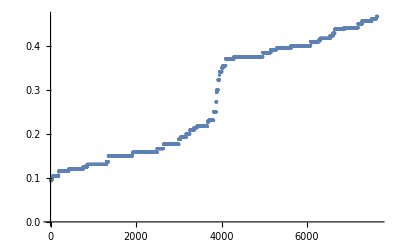

```mathematica
ListPlot[Sort[%]]
```

```mathematica
ListPlot[Sort[Map[#[[2]]/Total[#[[3]]]&,Select[mset,PrimePowerQ[#[[2]]]&]]]]
```

-Graphics-

```mathematica
Mean[Out[199]]
```

729975507195115934165081693980674571/11404310567789726762173970571600000000

```mathematica
N[%]
```

0.0640087

```mathematica
Min[Out[171]]
```

1/76

```mathematica
Max[Map[Total[#[[3]]]&,mset]]
```

76

```mathematica
mset[[1]][[3]]
```

```mathematica
minmod[{5,1,10,6,5,7,8,10},0]
```

{0,5,{5,1,10,6,5,7,8,10}}

```mathematica
3/8//N
```

```mathematica
ListPlot[Sort[%]]
```

-Graphics-

```mathematica
Mean[Map[tf[MemberQ[Divisors[Total[#[[3]]]],#[[2]]]]&,mset]]
```

301683/1000000

```mathematica
N[%]
```

0.301683

```mathematica
Total[Map[tf[PrimePowerQ[Total[#[[3]]]]]&,mset]]
```

309129

```mathematica
1-240405/1000000
```

151919/200000

```mathematica
minmod[list_,boolint_]:={boolint,Block[{w=2},While[parttest[list,w]==(boolint)⊻w<Total[list],w++];w],list}
```

```mathematica
minmod[sset[[1]],1]
```

{1,5,{32,4,73,100,85,76}}

```mathematica
False⊻True
```

True

```mathematica
minmod[sset[[1]],1]
```

{1,370,{32,4,73,100,85,76}}

```mathematica
2366/60//N
```

39.4333

```mathematica
Length[%]
```

31139

```mathematica
parttest[s_,t_]:=Block[{T3=DeleteCases[Map[Mod[#,t]&,s],0]},Block[{T3t=Total[Map[tf[Mod[Total[#],t]==Mod[Total[T3]/2,t]]&,Subsets[T3,{2}]]]},Piecewise[{{1, T3t>0}, {0, T3t==0}}]]]
```

```mathematica
Table[parttest[j,3],{j,sset}]
```

{1,1,0,1,0,1,1,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,1,1,0,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0,0,1,0,1,0,0,0,1,1,1,0,1,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1,1,1,0,1,0,1,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,30773,0,0,1,1,0,0,1,0,0,0,0,0,0,1,0,0,1,1,0,1,0,1,0,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,1,1,0,0,1,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,0,0,1,1,0,1,1,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,1,1,0,0,0,1,1,0,0,1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,1,0,1,0,1,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Select[sset,Mod[Total[#],3]==0&]
```

{{8,4,8,3,7},{6,2,5,9,8},{10,9,7,8,2},{3,10,7,2,8},{8,1,9,10,8},{7,1,9,9,10},{4,10,1,5,10},{7,1,7,8,7},{2,5,3,4,4},{6,1,6,2,9},{4,5,9,2,10},{9,10,2,6,9},{2,4,1,9,8},{4,6,8,3,9},{10,10,4,8,4},{7,7,1,5,4},{4,5,2,6,7},{2,1,5,10,6},{1,9,8,2,4},{2,8,2,3,9},{4,5,10,1,10},{3,2,4,5,10},{7,1,9,9,10},{2,6,2,6,8},{4,3,7,8,2},{5,2,7,1,9},{4,3,1,8,8},{7,5,3,3,6},{1,4,7,2,10},10239,{4,6,9,4,7},{1,4,3,2,2},{1,9,9,5,6},{7,9,8,2,4},{6,4,2,4,8},{9,8,6,2,5},{1,1,4,8,4},{7,5,5,4,3},{2,4,10,5,9},{4,8,3,3,6},{3,5,7,8,7},{4,4,1,2,7},{3,1,8,9,3},{3,6,7,5,3},{10,7,8,4,1},{8,5,2,5,10},{1,5,4,7,7},{2,9,7,1,5},{1,9,6,8,6},{3,4,2,3,6},{5,1,7,9,8},{3,5,3,4,3},{5,5,7,8,5},{5,2,2,5,4},{1,7,3,8,5},{5,3,10,4,8},{8,4,6,5,1},{3,8,3,9,7},{5,2,5,9,3}}
 |  |  |  |

```mathematica
sset[[3]]
```

{5,1,9,2,3}

```mathematica
Total[%]
```

```mathematica
Mod[20,3]
```

2

```mathematica
Map[Mod[#,4]&,{5,1,9,2,3}]
```

{1,1,1,2,3}

```mathematica
dptest[list_]:=Block[{pdiv=Select[Divisors[Total[list]],#>1&(*PrimeQ*)]},Map[parttest[list,#]&,pdiv]]
```

```mathematica
Length[sset]
```

262

```mathematica
Min[Flatten[Position[dptest[sset[[2]]],1]]]
```

3

```mathematica
Monitor[Table[Block[{dp=Total[dptest[sset[[i]]]]},Piecewise[{{{Min[Flatten[Position[dptest[sset[[i]]],1]]],Min[Flatten[Position[dptest[sset[[i]]],1]]]/Length[Select[Divisors[Total[sset[[i]]]],#>1&]],Divisors[Total[sset[[i]]]][[1+Min[Flatten[Position[dptest[sset[[i]]],1]]]]],FactorInteger[Total[sset[[i]]]]}, dp>0}, {0, dp≤0}}]],{i,1,Length[sset]}],i]
```

{{3,3/7,8,{{2,3},{23,1}}},{3,3/11,4,{{2,2},{3,1},{19,1}}},{1,1/7,2,{{2,1},{3,1},{41,1}}},{3,1,38,{{2,1},{19,1}}},{1,1/11,2,{{2,1},{3,1},{5,2}}},{3,3/11,4,{{2,2},{3,1},{19,1}}},{2,2/3,193,{{2,1},{193,1}}},{1,1/15,2,{{2,3},{3,1},{13,1}}},{3,1/5,5,{{2,1},{3,1},{5,1},{11,1}}},{3,3/19,4,{{2,4},{3,1},{5,1}}},{1,1/11,2,{{2,1},{3,2},{17,1}}},{2,2/3,113,{{2,1},{113,1}}},{3,3/17,4,{{2,5},{3,2}}},{2,2/3,197,{{2,1},{197,1}}},{2,2/3,109,{{2,1},{109,1}}},{1,1/11,2,{{2,1},{3,1},{7,2}}},{2,2/17,3,{{2,2},{3,2},{7,1}}},{1,1/15,2,{{2,3},{5,1},{7,1}}},{2,2/5,4,{{2,2},{53,1}}},{4,4/7,29,{{2,1},{3,1},{29,1}}},{2,2/5,4,{{2,2},{67,1}}},{2,2/7,5,{{2,1},{5,3}}},{1,1/7,2,{{2,1},{3,1},{59,1}}},{2,2/17,3,{{2,5},{3,2}}},{2,2/11,4,{{2,2},{7,1},{13,1}}},{5,5/11,11,{{2,2},{3,1},{11,1}}},{5,1,116,{{2,2},{29,1}}},{2,2/3,113,{{2,1},{113,1}}},{7,1,102,{{2,1},{3,1},{17,1}}},{2,2/3,67,{{2,1},{67,1}}},{5,5/7,26,{{2,1},{11,1},{13,1}}},{2,2/11,3,{{2,2},{3,1},{23,1}}},{1,1/7,2,{{2,1},{3,1},{19,1}}},{1,1/3,2,{{2,1},{163,1}}},{1,1/3,2,{{2,1},{157,1}}},{4,4/7,23,{{2,3},{23,1}}},{1,1/7,2,{{2,1},{5,3}}},{5,5/11,7,{{2,2},{3,1},{7,1}}},{2,2/11,4,{{2,2},{5,1},{7,1}}},{2,2/11,3,{{2,1},{3,2},{11,1}}},{2,2/3,83,{{2,1},{83,1}}},{5,1,92,{{2,2},{23,1}}},{5,5/17,8,{{2,5},{3,2}}},{1,1/8,2,{{2,8}}},{5,5/9,16,{{2,4},{11,1}}},{2,2/3,137,{{2,1},{137,1}}},{2,2/3,137,{{2,1},{137,1}}},{2,2/3,167,{{2,1},{167,1}}},{3,3/11,5,{{2,2},{5,1},{13,1}}},{1,1/15,2,{{2,3},{3,1},{11,1}}},{2,2/7,7,{{2,1},{7,1},{19,1}}},{5,5/7,62,{{2,1},{5,1},{31,1}}},{2,2/7,3,{{2,1},{3,1},{43,1}}},{2,2/7,5,{{2,1},{5,1},{23,1}}},{3,1,86,{{2,1},{43,1}}},{3,1/5,4,{{2,3},{3,3}}},{1,1/5,2,{{2,2},{53,1}}},{1,1/11,2,{{2,1},{3,2},{11,1}}},{2,2/3,83,{{2,1},{83,1}}},{1,1/5,2,{{2,2},{67,1}}},{2,2/5,13,{{2,1},{13,2}}},{1,1/15,2,{{2,7},{3,1}}},{3,3/11,5,{{2,3},{5,2}}},{2,2/5,4,{{2,2},{73,1}}},{3,3/7,6,{{2,1},{3,1},{61,1}}},{2,2/3,157,{{2,1},{157,1}}},{2,2/7,3,{{2,1},{3,1},{59,1}}},{2,2/3,151,{{2,1},{151,1}}},{2,2/3,163,{{2,1},{163,1}}},{3,3/7,10,{{2,1},{5,1},{11,1}}},{11,11/17,20,{{2,2},{3,2},{5,1}}},{3,3/7,10,{{2,1},{5,1},{31,1}}},{6,6/7,111,{{2,1},{3,1},{37,1}}},{2,2/11,3,{{2,1},{3,2},{19,1}}},{1,1/7,2,{{2,3},{19,1}}},{2,2/5,4,{{2,2},{31,1}}},{2,2/11,3,{{2,2},{3,1},{13,1}}},{3,1,122,{{2,1},{61,1}}},{1,1/9,2,{{2,4},{13,1}}},{3,3/8,8,{{2,8}}},{3,3/7,14,{{2,1},{7,1},{17,1}}},{2,2/19,3,{{2,4},{3,1},{5,1}}},{1,1/19,2,{{2,4},{3,1},{7,1}}},{2,2/19,3,{{2,4},{3,1},{7,1}}},{5,5/7,50,{{2,1},{5,3}}},{4,4/7,14,{{2,1},{7,1},{11,1}}},{3,1,194,{{2,1},{97,1}}},{7,1,154,{{2,1},{7,1},{11,1}}},{2,2/7,5,{{2,1},{5,1},{37,1}}},{2,2/3,149,{{2,1},{149,1}}},{1,1/7,2,{{2,3},{19,1}}},{11,11/13,64,{{2,6},{3,1}}},{2,2/15,3,{{2,1},{3,1},{5,1},{7,1}}},{3,3/5,71,{{2,2},{71,1}}},{2,2/3,113,{{2,1},{113,1}}},{1,1/7,2,{{2,1},{7,1},{23,1}}},{1,1/3,2,{{2,1},{83,1}}},{1,1/11,2,{{2,1},{3,1},{7,2}}},{1,1/9,2,{{2,4},{11,1}}},{1,1/8,2,{{2,8}}},{3,3/7,14,{{2,1},{7,1},{19,1}}},{3,3/11,6,{{2,1},{3,2},{7,1}}},{3,3/7,8,{{2,7}}},{2,2/3,101,{{2,1},{101,1}}},{1,1/3,2,{{2,1},{151,1}}},{4,4/15,6,{{2,3},{3,1},{11,1}}},{3,3/7,13,{{2,1},{11,1},{13,1}}},{1,1/7,2,{{2,3},{37,1}}},{3,3/11,7,{{2,5},{7,1}}},{2,2/5,4,{{2,2},{61,1}}},{5,1,76,{{2,2},{19,1}}},{7,1,138,{{2,1},{3,1},{23,1}}},{2,2/5,4,{{2,2},{61,1}}},{3,3/7,6,{{2,1},{3,1},{23,1}}},{2,2/7,4,{{2,3},{31,1}}},{1,1/5,2,{{2,2},{53,1}}},{1,1/7,2,{{2,3},{17,1}}},{1,1/8,2,{{2,2},{7,2}}},{2,2/11,3,{{2,2},{3,1},{19,1}}},{1,1/3,2,{{2,1},{137,1}}},{5,5/7,34,{{2,1},{7,1},{17,1}}},{1,1/15,2,{{2,3},{3,1},{13,1}}},{1,1/9,2,{{2,4},{19,1}}},{2,2/5,4,{{2,2},{89,1}}},{1,1/3,2,{{2,1},{107,1}}},{1,1/7,2,{{2,3},{31,1}}},{7,7/15,13,{{2,3},{3,1},{13,1}}},{2,2/7,5,{{2,1},{5,1},{29,1}}},{1,1/3,2,{{2,1},{83,1}}},{1,1/7,2,{{2,1},{5,3}}},{1,1/13,2,{{2,6},{3,1}}},{1,1/19,2,{{2,4},{3,1},{5,1}}},{1,1/11,2,{{2,1},{3,2},{19,1}}},{3,3/5,26,{{2,1},{13,2}}},{1,1/5,2,{{2,2},{19,1}}},{2,2/3,131,{{2,1},{131,1}}},{2,2/3,67,{{2,1},{67,1}}},{1,1/7,2,{{2,1},{7,1},{11,1}}},{1,1/5,2,{{2,2},{83,1}}},{1,1/15,2,{{2,3},{3,3}}},{1,1/5,2,{{2,2},{41,1}}},{2,2/7,5,{{2,1},{5,1},{11,1}}},{2,2/3,131,{{2,1},{131,1}}},{2,2/15,4,{{2,3},{5,1},{7,1}}},{3,3/7,8,{{2,3},{37,1}}},{2,2/3,101,{{2,1},{101,1}}},{2,2/3,131,{{2,1},{131,1}}},{3,1,118,{{2,1},{59,1}}},{3,3/11,6,{{2,1},{3,2},{17,1}}},{2,2/7,3,{{2,1},{3,1},{29,1}}},{2,2/7,3,{{2,1},{3,1},{43,1}}},{4,4/11,8,{{2,3},{5,2}}},{5,5/7,58,{{2,1},{5,1},{29,1}}},{1,1/17,2,{{2,5},{3,2}}},{2,1/4,4,{{2,8}}},{3,3/11,6,{{2,1},{3,2},{17,1}}},{5,5/8,28,{{2,2},{7,2}}},{3,3/5,59,{{2,2},{59,1}}},{1,1/7,2,{{2,1},{11,1},{13,1}}},{2,2/7,5,{{2,1},{5,1},{37,1}}},{1,1/11,2,{{2,1},{3,2},{11,1}}},{3,1,62,{{2,1},{31,1}}},{2,2/5,4,{{2,2},{43,1}}},{1,1/3,2,{{2,1},{137,1}}},{1,1/11,2,{{2,5},{11,1}}},{1,1/7,2,{{2,3},{31,1}}},{1,1/5,2,{{2,2},{61,1}}},{2,2/11,4,{{2,2},{5,1},{17,1}}},{1,1/15,2,{{2,3},{3,1},{7,1}}},{3,3/7,6,{{2,1},{3,1},{47,1}}},{2,2/11,3,{{2,5},{3,1}}},{1,1/7,2,{{2,1},{3,1},{47,1}}},{3,1,166,{{2,1},{83,1}}},{2,2/11,4,{{2,5},{7,1}}},{1,1/15,2,{{2,1},{3,1},{5,1},{7,1}}},{12,6/7,48,{{2,4},{3,2}}},{2,2/15,3,{{2,3},{3,1},{13,1}}},{3,1,158,{{2,1},{79,1}}},{6,6/7,95,{{2,1},{5,1},{19,1}}},{2,2/7,5,{{2,1},{5,1},{31,1}}},{1,1/11,2,{{2,2},{5,1},{17,1}}},{4,4/19,6,{{2,4},{3,1},{7,1}}},{2,2/5,11,{{2,1},{11,2}}},{1,1/11,2,{{2,2},{3,1},{23,1}}},{3,3/11,6,{{2,1},{3,2},{17,1}}},{2,2/5,4,{{2,2},{83,1}}},{2,2/3,151,{{2,1},{151,1}}},{2,2/7,4,{{2,3},{29,1}}},{2,2/3,149,{{2,1},{149,1}}},{1,1/5,2,{{2,2},{89,1}}},{17,1,180,{{2,2},{3,2},{5,1}}},{2,2/5,4,{{2,2},{53,1}}},{2,2/5,4,{{2,2},{43,1}}},{1,1/7,2,{{2,1},{7,1},{11,1}}},{2,2/11,3,{{2,2},{3,1},{7,1}}},{1,1/9,2,{{2,4},{19,1}}},{3,3/17,4,{{2,5},{3,2}}},{4,4/5,134,{{2,2},{67,1}}},{2,2/5,4,{{2,2},{59,1}}},{2,2/3,167,{{2,1},{167,1}}},{1,1/7,2,{{2,1},{11,1},{13,1}}},{2,2/3,79,{{2,1},{79,1}}},{1,1/15,2,{{2,3},{3,1},{13,1}}},{1,1/11,2,{{2,1},{3,2},{19,1}}},{4,4/7,29,{{2,3},{29,1}}},{2,2/3,83,{{2,1},{83,1}}},{1,1/7,2,{{2,1},{7,1},{13,1}}},{1,1/15,2,{{2,1},{3,3},{5,1}}},{3,3/7,14,{{2,1},{7,1},{19,1}}},{2,2/11,3,{{2,1},{3,2},{7,1}}},{2,2/7,5,{{2,1},{5,1},{17,1}}},{1,1/15,2,{{2,1},{3,1},{5,1},{13,1}}},{1,1/15,2,{{2,1},{3,1},{5,1},{7,1}}},{4,4/7,22,{{2,1},{11,1},{13,1}}},{2,2/7,4,{{2,3},{43,1}}},{3,3/5,67,{{2,2},{67,1}}},{3,3/7,8,{{2,3},{37,1}}},{1,1/11,2,{{2,1},{5,2},{7,1}}},{1,1/15,2,{{2,3},{3,1},{7,1}}},{4,4/7,47,{{2,1},{3,1},{47,1}}},{4,2/7,6,{{2,2},{3,4}}},{1,1/15,2,{{2,1},{3,1},{5,1},{7,1}}},{1,1/3,2,{{2,1},{79,1}}},{2,2/3,139,{{2,1},{139,1}}},{1,1/7,2,{{2,1},{5,1},{17,1}}},{1,1/5,2,{{2,2},{29,1}}},{3,3/7,14,{{2,1},{7,1},{19,1}}},{1,1/3,2,{{2,1},{181,1}}},{2,2/3,157,{{2,1},{157,1}}},{1,1/15,2,{{2,3},{3,3}}},{3,3/11,6,{{2,1},{3,2},{19,1}}},{2,2/3,97,{{2,1},{97,1}}},{1,1/7,2,{{2,1},{7,1},{19,1}}},{2,2/15,3,{{2,1},{3,1},{5,1},{11,1}}},{3,3/7,10,{{2,1},{5,1},{11,1}}},{1,1/11,2,{{2,1},{5,2},{7,1}}},{4,4/7,37,{{2,3},{37,1}}},{1,1/3,2,{{2,1},{163,1}}},{5,1/3,8,{{2,3},{3,1},{11,1}}},{2,2/5,11,{{2,1},{11,2}}},{1,1/17,2,{{2,2},{3,2},{5,1}}},{2,2/11,3,{{2,2},{3,1},{23,1}}},{1,1/7,2,{{2,1},{5,1},{19,1}}},{1,1/7,2,{{2,1},{5,1},{29,1}}},{2,2/7,5,{{2,1},{5,1},{17,1}}},{2,2/7,3,{{2,1},{3,1},{47,1}}},{1,1/5,2,{{2,2},{43,1}}},{1,1/15,2,{{2,7},{3,1}}},{6,6/7,91,{{2,1},{7,1},{13,1}}},{7,7/13,16,{{2,6},{3,1}}},{1,1/9,2,{{2,4},{19,1}}},{1,1/15,2,{{2,3},{3,1},{13,1}}},{1,1/9,2,{{2,4},{5,1}}},{2,2/5,4,{{2,2},{71,1}}},{2,2/7,5,{{2,1},{5,1},{29,1}}},{4,4/13,6,{{2,6},{3,1}}},{1,1/5,2,{{2,2},{61,1}}},{7,1,152,{{2,3},{19,1}}},{1,1/7,2,{{2,1},{5,1},{23,1}}},{2,2/3,139,{{2,1},{139,1}}},{2,2/7,4,{{2,3},{29,1}}},{3,3/5,73,{{2,2},{73,1}}}}

```mathematica
Map[#[[2]]&,%]
```

{3/7,3/11,1/7,1,1/11,3/11,2/3,1/15,1/5,3/19,1/11,2/3,3/17,2/3,2/3,1/11,2/17,1/15,2/5,4/7,2/5,2/7,1/7,2/17,2/11,5/11,1,2/3,1,2/3,5/7,2/11,1/7,1/3,1/3,4/7,1/7,5/11,2/11,2/11,2/3,1,5/17,1/8,5/9,2/3,2/3,2/3,3/11,1/15,2/7,5/7,2/7,2/7,1,1/5,1/5,1/11,2/3,1/5,2/5,1/15,3/11,2/5,3/7,2/3,2/7,2/3,2/3,3/7,11/17,3/7,6/7,2/11,1/7,2/5,2/11,1,1/9,3/8,3/7,2/19,1/19,2/19,5/7,4/7,1,1,2/7,2/3,1/7,11/13,2/15,3/5,2/3,1/7,1/3,1/11,1/9,1/8,3/7,3/11,3/7,2/3,1/3,4/15,3/7,1/7,3/11,2/5,1,1,2/5,3/7,2/7,1/5,1/7,1/8,2/11,1/3,5/7,1/15,1/9,2/5,1/3,1/7,7/15,2/7,1/3,1/7,1/13,1/19,1/11,3/5,1/5,2/3,2/3,1/7,1/5,1/15,1/5,2/7,2/3,2/15,3/7,2/3,2/3,1,3/11,2/7,2/7,4/11,5/7,1/17,1/4,3/11,5/8,3/5,1/7,2/7,1/11,1,2/5,1/3,1/11,1/7,1/5,2/11,1/15,3/7,2/11,1/7,1,2/11,1/15,6/7,2/15,1,6/7,2/7,1/11,4/19,2/5,1/11,3/11,2/5,2/3,2/7,2/3,1/5,1,2/5,2/5,1/7,2/11,1/9,3/17,4/5,2/5,2/3,1/7,2/3,1/15,1/11,4/7,2/3,1/7,1/15,3/7,2/11,2/7,1/15,1/15,4/7,2/7,3/5,3/7,1/11,1/15,4/7,2/7,1/15,1/3,2/3,1/7,1/5,3/7,1/3,2/3,1/15,3/11,2/3,1/7,2/15,3/7,1/11,4/7,1/3,1/3,2/5,1/17,2/11,1/7,1/7,2/7,2/7,1/5,1/15,6/7,7/13,1/9,1/15,1/9,2/5,2/7,4/13,1/5,1,1/7,2/3,2/7,3/5}

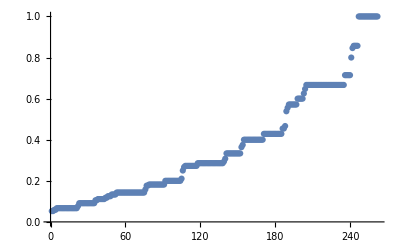

```mathematica
ListPlot[Sort[%]]
```

```mathematica
Mean[%]
```

447/131

```mathematica
N[%]
```

3.41221